### Required Functions (evaluate this cell first):

```mathematica
(* Produces an interpolation function that has a 'dimple' centered at the thump-point {Ax,Ay} inside of the parametrized border {{f,g},{umin,umax}} using Nbordpts number of border points;
- f,g are the *heads* of the border functions;
- Will NOT return an error if {Ax,Ay} is outside of the region *)
pluck[{{f_,g_},{umin_,umax_}},Nbordpts_][{Ax_,Ay_}]:=Module[{hmax,δ,γ,recurt,constructxy,oneline,datapts,recurtpoints,mesh},
hmax=1;
δ=.05;
(* γ:[0,1]->R^2 *)
γ[{x1_,y1_},{x2_,y2_}][t_]:= {(1-t)x1+t x2,(1-t)y1+t y2};
(* Constructs points for a line from (0,0) to (1,hmax) *)
recurt[{n_,t_,z_}]:={n+1,1-(1-t)/(hmax+δ/(n+1)-z)(2δ)/(n+1),hmax-δ/(n+1)};
recurtpoints=Join[NestList[recurt,{0,0,0},10],Table[{0,(1-(2δ)/(hmax+δ))i/4,(hmax+δ)(1-(2δ)/(hmax+δ))i/4},{i,1,3}]];
(* constructs points in R^3 from points recursively determined previously in recurt using a border point calculated from coordinate function heads f,g *)
constructxy[U_][{n_,t_,z_}]:={γ[{f[U],g[U]},{ax,ay}][t],-z};
(* Now define a function to create set of points {{x,y},z} along one line from {f[U],g[U]} to {ax,ay} - f,g need to be the *heads* of the coordinate functions e.g Cos,Sin NOT Cos[u],Sin[u] *)
oneline[Num_][U_]:=(Map[constructxy[U],recurtpoints]);
(* Essentially create these interpolation points for a bunch of lines from a bunch of different border points and put them all into one set, then interpolate 
hmax is Absolute value of maximum depth (default is 1)*)
datapts=(DeleteDuplicatesBy[Append[Flatten[Map[oneline[10],Range[umin,umax,(umax-umin)/Nbordpts]],1],{{ax,ay},-hmax}],First]/.{ax->Ax,ay->Ay});
(* This requires a random addition of a small amount to make sure that Mathematica does not mistake a triangle in the mesh as having zero area *)
mesh=NDSolve`FEM`ToElementMesh[datapts[[All,1]]+RandomReal[{-10^-9,10^-9},{Length[datapts]}]];
NDSolve`FEM`ElementMeshInterpolation[{mesh},datapts[[All,2]],InterpolationOrder->1]];

peak[δ_,{x0_,y0_}]:=Module[{A,σx,σy,Gaussian,region,tempts},
A=-1;
σx=δ;
σy=δ;
Gaussian[u_,v_]:=A Exp[-((u-x0)^2/(2 σx^2)+(v-y0)^2/(2 σy^2))];
Gaussian];

(* Produces a region from the parametrized border {f,g},{umin,umax};
-f,g are the *heads* of the border functions *)
parametricregion[{{f_,g_},{umin_,umax_}}]:=Module[{pts,plot},
plot=ParametricPlot[{f[u],g[u]},{u,umin,umax}];
pts=Flatten[Table[plot[[1,1,3,i,1]],{i,2,Length[Position[plot,Line]]+1}],1];
pts=DeleteDuplicates[pts];
BoundaryMeshRegion[pts,Line[Join[Range[Length[pts]-1],{1}]]]];

(* Determines the eigensystem up to Num'th eigenvalue for the given region *)
egsystem[Num_][region_]:=Module[{f,freqs,vals,funcs}, {vals,funcs}=NDEigensystem[{-Laplacian[f[x,y],{x,y}],DirichletCondition[f[x,y]==0,True]},{f},{x,y}∈region,Num];
freqs=√vals;
{freqs,funcs}]

(* Performs the numeric integral calculating the coefficents needed as fast as possible; 
-hit and eigenfunction are the heads of the functions *)
fastint[hit_,eigenfunction_]:=NIntegrate[hit[x,y]*eigenfunction[x,y],{x,y}∈eigenfunction["ElementMesh"],Method->{Automatic,"SymbolicProcessing"->0}]

reimannianint[region_,numberdiv_:50][hit_,eigenfunctionlist_]:=Module[{Δx,Δy,area,squaregrid,i,inside,heights,xmin,xmax,ymax,ymin,coord},
coord=region["Coordinates"];
xmax=Max[coord[[All,1]]];
xmin=Min[coord[[All,1]]];
ymax=Max[coord[[All,2]]];
ymin=Min[coord[[All,2]]];
Δx=(xmax-xmin)/numberdiv;
Δy=(ymax-ymin)/numberdiv;
area=Δx*Δy;
squaregrid=Flatten[Table[{x,y},
{x,xmin,xmax,Δx},
{y,ymin,ymax,Δy}],1];
inside={};
For[i=1,i≤Length[squaregrid],i++,
If[RegionMember[region,squaregrid[[i]]],
AppendTo[inside,squaregrid[[i]]],
False]];
heights=Table[Map[hit[#[[1]],#[[2]]]*eigenfunctionlist[[i]][#[[1]],#[[2]]]&,inside],{i,Length[eigenfunctionlist]}];
area*Map[Total,heights]]

(* VERY fast approximation that uses the Quadratic Order Triangle Rule *)
QOtriangleApprox2[hit_,efunclist_]:=Module[{emesh,indices,hitvals},
emesh=efunclist[[1]]["ElementMesh"];
indices=emesh["MeshElements"]/.{NDSolve`FEM`TriangleElement[t_]}:>Flatten@t[[All,4;;6]];
hitvals=hit[#[[1]],#[[2]]]&/@efunclist[[1]]["Grid"][[indices]];
Table[
Total[Total[Partition[hitvals*eigenfunction["ValuesOnGrid"][[indices]],3],{2}]*
First@eigenfunction["ElementMesh"]["MeshElementMeasure"]/3],
{eigenfunction,efunclist}]]
```

## Thumping

These functions are what I am using to calculate and display the frequencies and intensities for a specific thump location for a specific shape. You can look through the above code for the details, but you can see the general outline for the calculation in the freqsintens funciton:

Determine the region enclosed by the parametrized boundary

Calculate the eigenfuncitons and eigenvalues for the region

Calculate the resonant frequencies from the eigenvalues

Produce a “thump-shape” for a specifc point inside of the region

Calculate the coefficients of the eigenfunctions approximating this shape

Determine the intensities for each frequency from these coefficients (setting the maximum intensity at 1)

Integrating to calculate the coefficients of the eigenfuncitons is what is really slowing this funciton down. Also the “frequencies” that are output are not real-life values, but they should differ from a set of real-life values only by a scaling factor, so the differences between them should be preserved.
Also adding in an option to choose which type of hit to make.

```mathematica
(* - f,g need to be the heads of the border functions, umin,umax are the limits of the border parametrization, numberfreqs is the number of eigenfrequencies to find, thumpoints is the list of thumping points {{x1,y1},{x2,y2},...};- e.g freqsintens[{Cos,Sin},{0,2Pi},15][{{0,0}}] gives the first 15 eigenfrequencies of the circle with corresponding intensities when thumped at the point {0,0};- Uses parametricregion, egsystem,pluck, and fastint;
- Scales the intensities so that the fundamental has intensity 1;
- outputs a list in the form {{{freqlist1,intensitylist1},{freqlist2,intensitylist2},...},...}*)
freqsintens[{{f_,g_},{umin_,umax_}},numberfreqs_,method_:"Peak"][thumpoints_]/;
If[method=="Peak"||method=="Pluck",True,Message[freqsintens::fmethod,method];False]:=
Module[{region,funcs,freqs,thumps,coefs,intens},
region=parametricregion[{{f,g},{umin,umax}}];
{freqs,funcs}=egsystem[numberfreqs][region];
thumps=If[method=="Peak",
Table[peak[0.05,thumpoints[[i]]],{i,1,Length[thumpoints]}],
If[method=="Pluck",
Table[pluck[{{f,g},{umin,umax}},100][thumpoints[[i]]],{i,1,Length[thumpoints]}]],
Message];
coefs=Table[QOtriangleApprox2[thumps[[i]],funcs],{i,Length[thumps]}];
intens=Table[(coefs[[i,All]]/coefs[[i,1]])^2,{i,1,Length[coefs]}];
Table[{freqs[[All]],intens[[i,All]]},{i,1,Length[thumpoints]}]];
freqsintens::fmethod="Method `1` is not a valid method. Valid methods are: {Peak,Pluck}";

(* Same input as freqsintens but outputs a frequency vs intensity graph;
Uses a log scale on the y-axis, so it is easier to see all the frequencies
 **Uses freqsintens so will take just as long** *)
graphfi[{{f_,g_},{umin_,umax_}},numbervals_,method_:"Peak"][thumpoints_]:=Module[{list,fipairs},
list=freqsintens[{{f,g},{umin,umax}},numbervals,method][thumpoints];
fipairs=Table[{list[[i,1,x]],list[[i,2,x]]},{i,1,Length[thumpoints]},{x,1,Length[list[[1,2]]]}];
ListLogPlot[Table[Legended[fipairs[[i]],thumpoints[[i]]],{i,1,Length[thumpoints]}],Filling->Axis,PlotRange->All,AxesLabel->{Frequency,Intensity}]];
```

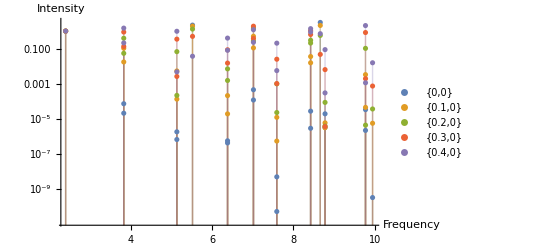

```mathematica
graphfi[{{Cos,Sin},{0,2Pi}},20][{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0}}]
```

### Examples:

Circle:

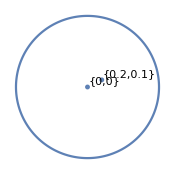
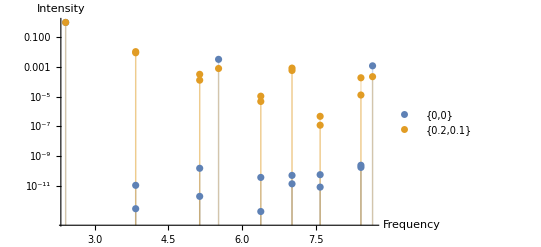

```mathematica
Module[{x,y,thumpts,umin,umax},
x[u_]:=Cos[u];
y[u_]:=Sin[u];
thumpts={{0,0},{0.2,0.1}};
umin=0;
umax=2Pi;
{Show[ParametricPlot[{x[u],y[u]},{u,umin,umax},Axes->False],ListPlot[Labeled[#,#]&/@thumpts,PlotStyle->PointSize[0.02],Axes->False]],
graphfi[{{x,y},{umin,umax}},15][thumpts]}]
```

Ellipse:

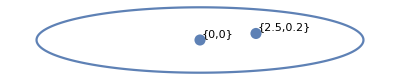
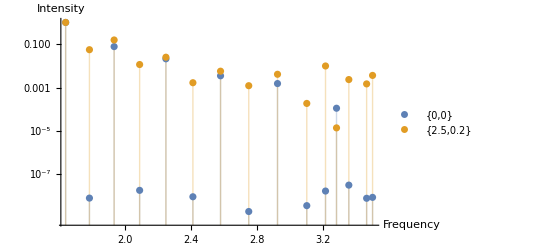

```mathematica
Module[{x,y,thumpts,umin,umax},
x[u_]:=7.3Cos[u];
y[u_]:=Sin[u];
thumpts={{0,0},{2.5,0.2}};
umin=0;
umax=2Pi;
{Show[ParametricPlot[{x[u],y[u]},{u,umin,umax},Axes->False],ListPlot[Labeled[#,#]&/@thumpts,PlotStyle->PointSize[0.02],Axes->False]],
graphfi[{{x,y},{umin,umax}},15][thumpts]}]
```

Square:

```mathematica
Module[{x,y,thumpoint,umin,umax,p},
p[V_][t_]:=Module[{ℓ},
ℓ[i_][t0_]:={(1-t0)V[[i,1]]+t0 V[[i+1,1]],(1-t0)V[[i,2]]+t0 V[[i+1,2]]};
ℓ[1][t]+Sum[UnitStep[t-i+1](ℓ[i][t-i+1]-ℓ[i-1][t-i+2]),{i,2,Length[V]-1}]];
x[ϵ_][t_]:=p[{{0,0},{1,0},{1+ϵ,1},{ϵ,1},{0,0}}][t][[1]];
y[ϵ_][t_]:=p[{{0,0},{1,0},{1+ϵ,1},{ϵ,1},{0,0}}][t][[2]];
thumpoint[ϵ_]:={{0.5+ϵ/2,0.5},{0.5+ϵ/2+0.2,0.5+0.2}};
umin=0;
umax=4;
graphic[ϵ_]:={Show[ParametricPlot[{x[ϵ][u],y[ϵ][u]},{u,umin,umax},Axes->False],ListPlot[Labeled[#,#]&/@thumpoint[ϵ],PlotStyle->PointSize[0.02],Axes->False]],
graphfi[{{x[ϵ],y[ϵ]},{umin,umax}},15][thumpoint[ϵ]]};]
```

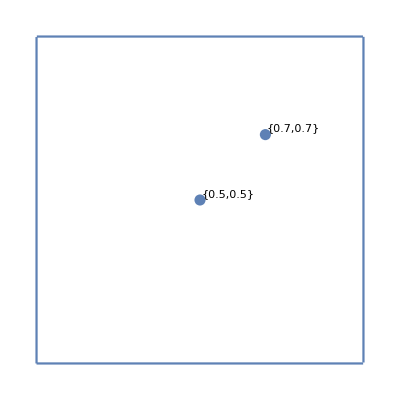
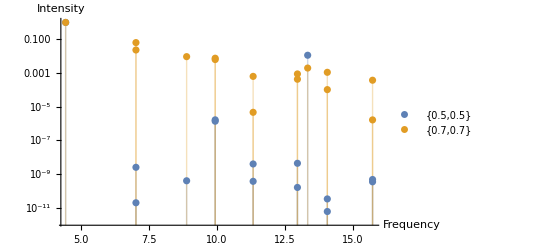

```mathematica
graphic[0]
```

Parallelogram:

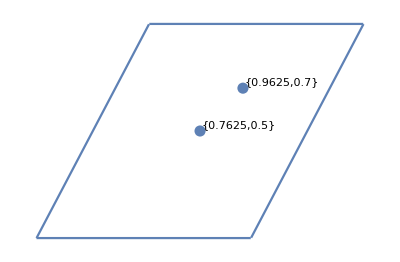
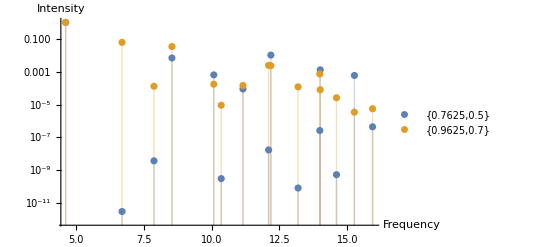

```mathematica
graphic[0.525]
```

This shows basically what we already know: that changing the border shape moves the fundamental freqeuncies around and changing the thumping location effects the intensiteis.

### Comparison Examples (Used as comparison to measured data):

Circle:

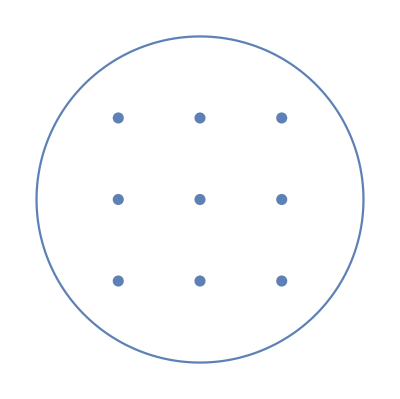

```mathematica
Module[{gridpts,gridplot},
gridpts={{0,0},{0,0.5},{0,-0.5},{-0.5,0},{0.5,0},{0.5,0.5},{0.5,-0.5},{-0.5,0.5},{-0.5,-0.5}};
gridplot=Show[ParametricPlot[{Cos[u],Sin[u]},{u,0,2Pi},Axes->False],ListPlot[gridpts,PlotStyle->PointSize[0.02],Axes->False]];
circlefipeak=freqsintens[{{Cos,Sin},{0,2Pi}},15,"Peak"][gridpts];
circlefipluck=freqsintens[{{Cos,Sin},{0,2Pi}},15,"Pluck"][gridpts];
gridplot]
```

```mathematica
gridpts={{0,0},{0,0.5},{0,-0.5},{-0.5,0},{0.5,0},{0.5,0.5},{0.5,-0.5},{-0.5,0.5},{-0.5,-0.5}};
Export["/Users/tomeichlersmith/Desktop/CircleGrid.jpg",Show[ParametricPlot[{Cos[u],Sin[u]},{u,0,2Pi}],ListPlot[gridpts,PlotStyle->PointSize[0.02]]]]
```

/Users/tomeichlersmith/Desktop/CircleGrid.jpg

```mathematica
(*Peak*)
Module[{gridpts,data,datatable},
gridpts={{0,0},{0,0.5},{0,-0.5},{-0.5,0},{0.5,0},{0.5,0.5},{0.5,-0.5},{-0.5,0.5},{-0.5,-0.5}};
data=Join[{circlefipeak[[1,1]]},Table[circlefipeak[[i,2]],{i,1,Length[circlefipeak]}]];
Print[MatrixForm[data]];
Export["/Users/tomeichlersmith/Desktop/temporary.xlsx",data]]
```

(2.40492 | 3.8319 | 3.83191 | 5.136 | 5.13613 | 5.52071 | 6.38116 | 6.38118 | 7.01721 | 7.01726 | 7.59039 | 7.59057 | 8.42116 | 8.42152 | 8.65846
1. | 1.12711×10^-9 | 4.2753×10^-8 | 2.45084×10^-10 | 2.99708×10^-8 | 2.18833 | 5.1645×10^-9 | 2.59209×10^-8 | 3.11102×10^-7 | 2.61225×10^-8 | 8.22373×10^-8 | 2.13299×10^-8 | 3.22535×10^-7 | 1.39937×10^-7 | 3.07763
1. | 2.13241 | 0.310414 | 2.03638 | 0.0120632 | 0.138791 | 1.21391 | 0.228437 | 0.179595 | 0.0345939 | 0.029003 | 0.884218 | 0.508681 | 0.804992 | 0.869417
1. | 2.13161 | 0.310288 | 2.03494 | 0.0120896 | 0.138426 | 1.21365 | 0.227904 | 0.180655 | 0.0347182 | 0.0292301 | 0.884498 | 0.508021 | 0.806737 | 0.872503
1. | 0.310408 | 2.1315 | 2.03504 | 0.0121442 | 0.138163 | 0.22783 | 1.21377 | 0.034938 | 0.180479 | 0.0291186 | 0.884189 | 0.506013 | 0.811014 | 0.872968
1. | 0.310765 | 2.13117 | 2.0354 | 0.0122794 | 0.138086 | 0.227242 | 1.21499 | 0.0351119 | 0.180694 | 0.0295451 | 0.884464 | 0.505428 | 0.811667 | 0.867211
1. | 3.29355 | 0.660282 | 0.0318359 | 5.39709 | 2.23109 | 5.45547 | 0.850193 | 3.07026 | 0.465056 | 0.210263 | 6.42151 | 1.3102 | 0.821413 | 0.632147
1. | 0.661076 | 3.29377 | 0.0315272 | 5.39814 | 2.23598 | 0.846969 | 5.46188 | 0.467343 | 3.08094 | 0.206514 | 6.42558 | 1.31334 | 0.830925 | 0.644662
1. | 0.660186 | 3.29419 | 0.0320282 | 5.39707 | 2.23453 | 0.851196 | 5.45626 | 0.465201 | 3.07731 | 0.210725 | 6.42221 | 1.31748 | 0.819562 | 0.652124
1. | 3.29411 | 0.660265 | 0.0319941 | 5.39863 | 2.23242 | 5.45723 | 0.851765 | 3.07764 | 0.466143 | 0.211247 | 6.42249 | 1.31486 | 0.82828 | 0.654565)

/Users/tomeichlersmith/Desktop/temporary.xlsx

```mathematica
(*Pluck*)
Module[{gridpts,data,datatable},
gridpts={{0,0},{0,0.5},{0,-0.5},{-0.5,0},{0.5,0},{0.5,0.5},{0.5,-0.5},{-0.5,0.5},{-0.5,-0.5}};
data=Join[{circlefipluck[[1,1]]},Table[circlefipluck[[i,2]],{i,1,Length[circlefipluck]}]];
Print[MatrixForm[data]];
Export["/Users/tomeichlersmith/Desktop/temporary.xlsx",data]]
```

(2.40492 | 3.8319 | 3.83191 | 5.136 | 5.13613 | 5.52071 | 6.38116 | 6.38118 | 7.01721 | 7.01726 | 7.59039 | 7.59057 | 8.42116 | 8.42152 | 8.65846
1. | 1.05135×10^-11 | 2.7834×10^-13 | 1.89207×10^-12 | 1.48141×10^-10 | 0.00325625 | 1.80629×10^-13 | 3.58527×10^-11 | 4.90773×10^-11 | 1.32377×10^-11 | 7.96758×10^-12 | 5.47209×10^-11 | 2.3639×10^-10 | 1.69765×10^-10 | 0.00118979
1. | 0.0747358 | 0.0108792 | 0.00807981 | 0.0000478845 | 0.00466396 | 0.000981249 | 0.000184185 | 1.43109×10^-6 | 2.67415×10^-7 | 6.975×10^-6 | 0.000209514 | 0.00011099 | 0.00017618 | 0.0000163993
1. | 0.0747337 | 0.0108818 | 0.00808114 | 0.0000478083 | 0.00466239 | 0.00098149 | 0.00018516 | 1.50954×10^-6 | 2.64398×10^-7 | 6.82158×10^-6 | 0.000210272 | 0.000110934 | 0.000177373 | 0.0000164846
1. | 0.010878 | 0.0747381 | 0.00808441 | 0.0000478507 | 0.00465964 | 0.000184796 | 0.000981777 | 2.90727×10^-7 | 1.46294×10^-6 | 6.85748×10^-6 | 0.000209834 | 0.000110971 | 0.000176578 | 0.0000166773
1. | 0.0108822 | 0.074732 | 0.00808271 | 0.0000482051 | 0.00465981 | 0.000184899 | 0.000980575 | 2.93079×10^-7 | 1.49351×10^-6 | 6.77635×10^-6 | 0.000209658 | 0.000110825 | 0.000177086 | 0.0000163296
1. | 0.119102 | 0.0238544 | 0.000127495 | 0.0214546 | 0.0231288 | 0.00417699 | 0.000650869 | 0.00580815 | 0.000877797 | 0.0000447829 | 0.00138278 | 0.000586223 | 0.000366753 | 0.00117172
1. | 0.0238606 | 0.119054 | 0.000127511 | 0.0214278 | 0.0231311 | 0.000652028 | 0.00416911 | 0.00087978 | 0.00580727 | 0.0000455134 | 0.00137615 | 0.000583823 | 0.000366968 | 0.00117652
1. | 0.0238622 | 0.119077 | 0.000127127 | 0.0214303 | 0.0231328 | 0.000648925 | 0.00416669 | 0.000878343 | 0.00580328 | 0.0000447331 | 0.00137814 | 0.000582849 | 0.000365036 | 0.00117969
1. | 0.119081 | 0.0238664 | 0.000126696 | 0.0214478 | 0.0231246 | 0.00417278 | 0.000648566 | 0.00580931 | 0.000878791 | 0.000045121 | 0.00137844 | 0.000585173 | 0.000368874 | 0.00118045)

/Users/tomeichlersmith/Desktop/temporary.xlsx

Square:

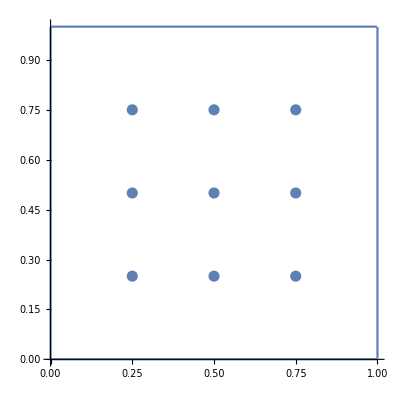

```mathematica
Module[{gridpts,gridplot,x,y,p},
p[V_][t_]:=Module[{ℓ},
ℓ[i_][t0_]:={(1-t0)V[[i,1]]+t0 V[[i+1,1]],(1-t0)V[[i,2]]+t0 V[[i+1,2]]};
ℓ[1][t]+Sum[UnitStep[t-i+1](ℓ[i][t-i+1]-ℓ[i-1][t-i+2]),{i,2,Length[V]-1}]];
x[t_]:=p[{{0,0},{1,0},{1,1},{0,1},{0,0}}][t][[1]];
y[t_]:=p[{{0,0},{1,0},{1,1},{0,1},{0,0}}][t][[2]];
gridpts=Flatten[Table[{i/4,j/4},{i,1,3},{j,1,3}],1];
gridplot=Show[ParametricPlot[{x[u],y[u]},{u,0,4}],ListPlot[gridpts,PlotStyle->PointSize[0.02]]];
Export["/Users/tomeichlersmith/Desktop/Summer Research 2016/SquareGrid.jpg",gridplot];
squarefipeak=freqsintens[{{x,y},{0,4}},15,"Peak"][gridpts];
squarefipluck=freqsintens[{{x,y},{0,4}},15,"Pluck"][gridpts];
gridplot]
```

```mathematica
Flatten[Table[{i/4,j/4},{i,1,3},{j,1,3}],1]
```

{{1/4,1/4},{1/4,1/2},{1/4,3/4},{1/2,1/4},{1/2,1/2},{1/2,3/4},{3/4,1/4},{3/4,1/2},{3/4,3/4}}

```mathematica
(*Peak*)
Module[{data},
data=Join[{squarefipeak[[1,1]]},Table[squarefipeak[[i,2]],{i,1,Length[squarefipeak]}]];
Print[MatrixForm[data]];
Export["/Users/tomeichlersmith/Desktop/temporary.xlsx",data]]
```

(4.4429 | 7.02495 | 7.02496 | 8.88621 | 9.9353 | 9.93533 | 11.3286 | 11.3287 | 12.9557 | 12.9559 | 13.3319 | 14.0534 | 14.0536 | 15.7148 | 15.715
1. | 0.991474 | 2.72313 | 3.44941 | 0.746949 | 0.894982 | 0.0226691 | 3.02648 | 9.80937×10^-8 | 2.78512×10^-8 | 0.672943 | 2.34367×10^-9 | 1.45288×10^-7 | 2.95142×10^-7 | 3.0509×10^-6
1. | 1.75021 | 0.107108 | 3.2531×10^-9 | 0.895088 | 0.746819 | 0.63133 | 0.893086 | 2.17427×10^-8 | 4.19178×10^-8 | 0.673825 | 4.914×10^-8 | 8.00004×10^-9 | 3.19131×10^-9 | 1.93512×10^-6
1. | 2.72304 | 0.991441 | 3.44918 | 0.746426 | 0.894728 | 3.02517 | 0.0226196 | 2.73271×10^-7 | 2.6527×10^-7 | 0.673528 | 1.28078×10^-7 | 8.50283×10^-9 | 6.56261×10^-7 | 9.75605×10^-8
1. | 0.107084 | 1.75024 | 5.60507×10^-10 | 0.894926 | 0.746752 | 0.893078 | 0.631554 | 1.38243×10^-8 | 2.36046×10^-7 | 0.673386 | 2.04743×10^-8 | 1.01434×10^-8 | 4.39811×10^-7 | 2.0079×10^-7
1. | 7.06164×10^-10 | 1.17876×10^-9 | 6.48331×10^-10 | 0.746789 | 0.894859 | 2.62568×10^-8 | 9.32105×10^-10 | 4.26146×10^-8 | 3.21776×10^-7 | 0.673678 | 1.03698×10^-7 | 1.73829×10^-11 | 2.18212×10^-7 | 4.60611×10^-9
1. | 0.107082 | 1.75022 | 1.29117×10^-10 | 0.894881 | 0.746736 | 0.892919 | 0.631346 | 5.85925×10^-8 | 5.77358×10^-10 | 0.673693 | 6.20675×10^-8 | 3.9671×10^-12 | 4.61854×10^-8 | 2.54366×10^-6
1. | 2.72316 | 0.991436 | 3.44969 | 0.746805 | 0.894739 | 3.0262 | 0.0226111 | 9.81693×10^-8 | 1.18879×10^-8 | 0.673153 | 5.40809×10^-7 | 4.24741×10^-8 | 2.39015×10^-6 | 1.54664×10^-7
1. | 1.75014 | 0.107109 | 4.05253×10^-9 | 0.894796 | 0.74672 | 0.631565 | 0.893038 | 3.00774×10^-10 | 3.76197×10^-8 | 0.673809 | 1.03575×10^-8 | 8.18286×10^-9 | 6.70367×10^-9 | 1.6477×10^-6
1. | 0.991499 | 2.72319 | 3.4496 | 0.746945 | 0.894854 | 0.0226386 | 3.02626 | 3.82218×10^-8 | 1.18902×10^-7 | 0.673758 | 3.38112×10^-8 | 2.52684×10^-8 | 9.59738×10^-8 | 2.25735×10^-7)

/Users/tomeichlersmith/Desktop/temporary.xlsx

```mathematica
(*Pluck*)
Module[{gridpts,data,datatable},
gridpts={{0,0},{0,0.5},{0,-0.5},{-0.5,0},{0.5,0},{0.5,0.5},{0.5,-0.5},{-0.5,0.5},{-0.5,-0.5}};
data=Join[{squarefipluck[[1,1]]},Table[squarefipluck[[i,2]],{i,1,Length[squarefipluck]}]];
Print[MatrixForm[data]];
Export["/Users/tomeichlersmith/Desktop/temporary.xlsx",data]]
```

(4.4429 | 7.02495 | 7.02496 | 8.88621 | 9.9353 | 9.93533 | 11.3286 | 11.3287 | 12.9557 | 12.9559 | 13.3319 | 14.0534 | 14.0536 | 15.7148 | 15.715
1. | 0.0325403 | 0.0894038 | 0.0182669 | 0.01294 | 0.0155092 | 5.01739×10^-7 | 0.0000628568 | 0.00185969 | 0.00383893 | 0.00170897 | 0.000318483 | 0.0000301156 | 3.4738×10^-7 | 0.0000755101
1. | 0.0643677 | 0.00393555 | 8.37573×10^-10 | 0.0134966 | 0.000351658 | 0.00284223 | 0.00401363 | 0.00235831 | 0.0000763724 | 0.00106676 | 1.85277×10^-9 | 6.62348×10^-10 | 0.000569497 | 0.000749415
1. | 0.0894258 | 0.0325527 | 0.0182654 | 0.012946 | 0.0155178 | 0.0000624894 | 5.32019×10^-7 | 0.00384284 | 0.0018637 | 0.00171005 | 0.000316554 | 0.0000286065 | 0.0000769683 | 3.16852×10^-7
1. | 0.00393785 | 0.0643653 | 1.47548×10^-9 | 0.0000672872 | 0.0137844 | 0.0040131 | 0.00283934 | 0.0000750534 | 0.00235955 | 0.00106474 | 6.42169×10^-11 | 6.4206×10^-11 | 0.000748866 | 0.000573674
1. | 2.45942×10^-9 | 1.91943×10^-11 | 3.88856×10^-10 | 1.34943×10^-6 | 1.62524×10^-6 | 3.87795×10^-9 | 3.60737×10^-10 | 1.56222×10^-10 | 4.26068×10^-9 | 0.0112303 | 3.24246×10^-11 | 5.79766×10^-12 | 3.3744×10^-10 | 4.63399×10^-10
1. | 0.00394235 | 0.0643567 | 4.93095×10^-10 | 0.0000665863 | 0.0137723 | 0.0040246 | 0.00284295 | 0.0000746258 | 0.00235187 | 0.00106369 | 7.11908×10^-10 | 5.02756×10^-11 | 0.000748129 | 0.000567905
1. | 0.0893855 | 0.0325727 | 0.0182574 | 0.0129313 | 0.015524 | 0.000062789 | 4.1509×10^-7 | 0.00383909 | 0.00187034 | 0.00171018 | 0.000315316 | 0.0000303014 | 0.0000780819 | 4.08002×10^-7
1. | 0.0643647 | 0.00394113 | 5.57934×10^-10 | 0.0135067 | 0.000352302 | 0.00284161 | 0.00401965 | 0.00235988 | 0.0000754305 | 0.00106519 | 4.90832×10^-9 | 2.62036×10^-9 | 0.000572808 | 0.000747534
1. | 0.0325499 | 0.089435 | 0.0182664 | 0.0129464 | 0.0155116 | 5.46854×10^-7 | 0.0000628829 | 0.00185958 | 0.00383026 | 0.00171481 | 0.000317798 | 0.0000298224 | 3.80706×10^-7 | 0.0000764856)

/Users/tomeichlersmith/Desktop/temporary.xlsx

Circle (to scale)